```mathematica
L =3;
```

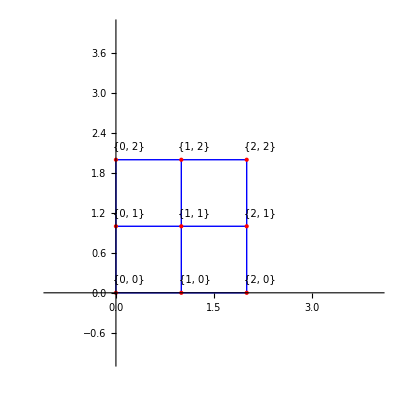

```mathematica
Graphics[
Module[{points,lines},
points=Flatten[Table[{m,n},{m,0,L-1},{n,0,L-1}],1];
lines=Select[Subsets[points,{2}],ManhattanDistance @@#==1&];
labels=Table[Text[Style[ToString[{m,n}],10],{m+0.2,n+0.2}],{m,0,L-1},{n,0,L-1}];
{Blue,Line/@ lines,Red, PointSize[Large],Point/@points,Black,Flatten[labels]}
],
Axes -> True,
AxesOrigin->{0,0},
PlotRange->{{-1,L+1},{-1,L+1}},
AspectRatio->1
]
```

```mathematica
horizontalBonds=Table[{{m,n},{m+1,n}},{m,0,L-2},{n,0,L-1}];
verticalBonds=Table[{{m,n},{m,n+1}},{m,0,L-1},{n,0,L-2}];

bonds=Join[Flatten[horizontalBonds,1],Flatten[verticalBonds,1]];
bonds
```

{{{0,0},{1,0}},{{0,1},{1,1}},{{0,2},{1,2}},{{1,0},{2,0}},{{1,1},{2,1}},{{1,2},{2,2}},{{0,0},{0,1}},{{0,1},{0,2}},{{1,0},{1,1}},{{1,1},{1,2}},{{2,0},{2,1}},{{2,1},{2,2}}}

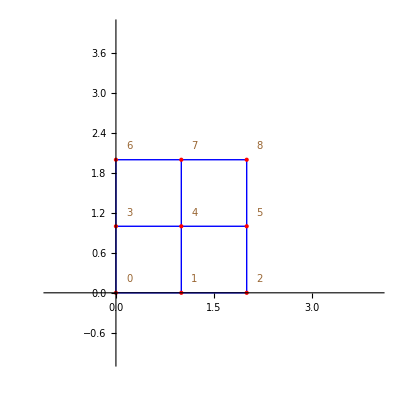

```mathematica
(*Generate lattice points with unique integer labels*)
points=Flatten[Table[{m,n},{n,0,L-1},{m,0,L-1}],1];

(*Assign an index to each point*)
indexedPoints=AssociationThread[points->Range[0,Length[points]-1]];

(*Horizontal and vertical bonds*)
horizontalBonds=Table[{{m,n},{m+1,n}},{m,0,L-2},{n,0,L-1}];
verticalBonds=Table[{{m,n},{m,n+1}},{m,0,L-1},{n,0,L-2}];
bonds=Join[Flatten[horizontalBonds,1],Flatten[verticalBonds,1]];

(*Plot with numbered labels*)
Graphics[{Blue,Line/@bonds,Red,PointSize[Large],Point/@Keys[indexedPoints],Brown,Table[Text[Style[ToString[indexedPoints[{m,n}]],10],{m+0.2,n+0.2}],{m,0,L-1},{n,0,L-1}]//Flatten},Axes->True,AxesOrigin->{0,0},PlotRange->{{-1,L+1},{-1,L+1}},AspectRatio->1]
```

```mathematica
(*Convert bonds to integer-labeled format*)
indexMap=AssociationThread[points->Range[0,Length[points]-1]];
integerBonds=Sort/@(indexMap/@#&/@bonds);
integerBonds
Length[integerBonds]
```

{{0,1},{3,4},{6,7},{1,2},{4,5},{7,8},{0,3},{3,6},{1,4},{4,7},{2,5},{5,8}}

12

```mathematica
(*periodicity*)
siteIndex[m_,n_]:=Mod[m,L]+L*Mod[n,L];

(*Generates all horizontal or vertical bonds*)
generateBonds[dir_,periodic_]:=Module[{rangeM,rangeN,pairFn},If[dir==="horizontal",rangeM=If[periodic,Range[0,L-1],Range[0,L-2]];
rangeN=Range[0,L-1];
pairFn={siteIndex[#,#2],siteIndex[#+1,#2]}&;,rangeM=Range[0,L-1];
rangeN=If[periodic,Range[0,L-1],Range[0,L-2]];
pairFn={siteIndex[#,#2],siteIndex[#,#2+1]}&;];
Sort/@Flatten[Table[pairFn[m,n],{n,rangeN},{m,rangeM}],1]];

(*Bonds for each case*)
bondsPBCm=Join[generateBonds["horizontal",True],generateBonds["vertical",False]];
bondsPBCn=Join[generateBonds["horizontal",False],generateBonds["vertical",True]];
bondsPBCboth=Join[generateBonds["horizontal",True],generateBonds["vertical",True]];

(*Output*)
Print["PBC in m only:"];
bondsPBCm//Print;
Length[bondsPBCm]//Print;

Print["PBC in n only:"];
bondsPBCn//Print;
Length[bondsPBCn]//Print;

Print["PBC in both m and n:"];
bondsPBCboth//Print;
Length[bondsPBCboth]//Print;
```

PBC in m only:

{{0,1},{1,2},{0,2},{3,4},{4,5},{3,5},{6,7},{7,8},{6,8},{0,3},{1,4},{2,5},{3,6},{4,7},{5,8}}

15

PBC in n only:

{{0,1},{1,2},{3,4},{4,5},{6,7},{7,8},{0,3},{1,4},{2,5},{3,6},{4,7},{5,8},{0,6},{1,7},{2,8}}

15

PBC in both m and n:

{{0,1},{1,2},{0,2},{3,4},{4,5},{3,5},{6,7},{7,8},{6,8},{0,3},{1,4},{2,5},{3,6},{4,7},{5,8},{0,6},{1,7},{2,8}}

18